Construct a Diagram for Heat Generation and Conduction through Composite Walls

```mathematica
Manipulate[
Module[{Qdot,Rtc,kA,kB,kC,wall,T∞,h,qflux,sol,T,Ts1,Ts2,Ts3,Ts4,Ts5,Ts6,TProfile,TA,TB,TC,T1,T2,colA,colB,colC,pt1},
SeedRandom[reset];
Qdot=RandomInteger[{4,6}];(*kW/m3*)
Rtc=N@RandomInteger[{0,8}]/100;(*m2 K/W*)
kA=N@RandomInteger[{15,25}]/100;kB=N@RandomInteger[{10,15}]/100;kC=N@RandomInteger[{45,55}]/100;(*W/m/K*)
LA=N@RandomInteger[{15,25}]/1000;LB=N@RandomInteger[{15,25}]/1000;LC=N@RandomInteger[{15,25}]/1000;(*m*)
(*wall=RandomInteger[{1,3}];*)
wall=RandomChoice[{1,2,3}];

T∞=20;(*°C*)h=10;(*W/m2/K*)qflux=1000*Qdot*If[wall==1,LA,LB];

(*sol=DSolve[{
t''[z]==-1000*Qdot/If[wall==1,kA,kB],
t[If[wall==1,LA,LA+LB]]==If[wall==1,Ts5,Ts3],
t'[If[wall==1,0,LA]]==0
},t[z],z][[1]];*)
sol=DSolve[{
t''[z]==-1000*Qdot/Switch[wall,1,kA,2,kB,3,kC],
t[Switch[wall,1,LA,2,LA+LB,3,LA+LB+LC]]==Switch[wall,1,Ts5,2,Ts3,3,Ts1],
t'[Switch[wall,1,0,2,LA,3,LB]]==0
},t[z],z][[1]];
T[x_]:=(t[z]/.sol)/.z->x;

Ts1=T∞+qflux/h;
(*Ts2=If[wall==3,Table[{n,T[n/1000]},{n,1000*(LA+LB),1000*(LA+LB+LC),1}],Ts1+qflux*LC/kC];*)
Ts2={1000*(LA+LB),Ts1+qflux*LC/kC};
Ts3=Ts2[[2]]+qflux*Rtc;
(*Ts4=If[wall==1,{1000*LA,Ts3+qflux*LB/kB},Table[{n(*+2*),T[n/1000]},{n,LA*1000,1000*(LA+LB),1}]];*)
Ts4=If[wall==2,Table[{n,T[n/1000]},{n,1000*LA,1000*(LA+LB),1}],{1000*LA,Ts3+qflux*LB/kB}];
Ts5=If[wall==1,Ts4[[2]]+qflux*Rtc,T[LA]];
Ts6=If[wall==1,Table[{n,T[n/1000]},{n,0,1000*LA,1}],{0,T[LA]}];

TProfile=Level[{Ts6,{1000*LA,Ts5},Ts4,{1000*(LA+LB),Ts3},{1000*(LA+LB),Ts2},{1000*(LA+LB+LC),Ts1}},{-2}];
TA=Join[If[wall==1,Ts6,{Ts6}],{{1000*LA,Ts5}}];
TB=Join[If[wall==2,Ts4,{Ts4}],{{1000*(LA+LB),Ts3}}];
(*TC={{1000*(LA+LB),Ts2},{1000*(LA+LB+LC),Ts1}};*)
TC=Join[If[wall==3,Table[{n,T[n/1000]},{n,1000*(LA+LB),1000*(LA+LB+LC),1}],{Ts2}],{{1000*(LA+LB+LC),Ts1}}];

T1=25;T2=125;

colA=RGBColor[0.25,0.8,0.9];colB=RGBColor[0.45,0.9,0];colC=RGBColor[1,0.95,0];
pt1[pt_,col_]:={col,PointSize@0.025,Point@pt,White,PointSize@0.015,Point@pt};

A1={0,A1[[2]]};A2={500*LA,A2[[2]]};A3={1000*LA,A3[[2]]};
B1={1000*LA,B1[[2]]};B2={1000*(LA+0.5*LB),B2[[2]]};B3={1000*(LA+LB),B3[[2]]};
C1={1000*(LA+LB),C1[[2]]};C2={1000*(LA+LB+0.5*LC),C2[[2]]};C3={1000*(LA+LB+LC),C3[[2]]};

Graphics[{
{EdgeForm@Black,FaceForm@colA,Rectangle[{0,T1},{LA*1000,T2}]},
{EdgeForm@Black,FaceForm@colB,Rectangle[{LA*1000,T1},{1000*(LA+LB),T2}]},
{EdgeForm@Black,FaceForm@colC,Rectangle[{1000*(LA+LB),T1},{1000*(LA+LB+LC),T2}]},
{EdgeForm@Thickness@0.015,FaceForm@None,Switch[wall,1,Rectangle[{0,T1},{1000*LA,T2}],2,Rectangle[{1000*LA,T1},{1000*(LA+LB),T2}],3,Rectangle[{1000*(LA+LB),T1},{1000*(LA+LB+LC),T2}]]},

Text[Style[Column[{Row@{Subscript[Style["k",Italic],#1]," = ",#2},"W/[m K]"},Center],17],{#3,T2-10}]&@@@{{"A",kA,500*LA},{"B",kB,1000*LA+500*LB},{"C",kC,1000*(LA+LB)+500*LC}},

{Thin,Line[{{0,T1-7},{1000*(LA+LB+LC),T1-7}}],Line[{{1000*#,T1-4},{1000*#,T1-10}}]&/@{0,LA,LA+LB,LA+LB+LC}},
Text[Framed[Style[Row@{1000*#1," mm"},17],Background->White,FrameStyle->None],{1000*#2,T1-7}]&@@@{{LA,0.5*LA},{LB,LA+0.5*LB},{LC,LA+LB+0.5*LC}},

Thick,CapForm@None,
If[CS==1,{
If[solution,{Thickness@0.007,Purple,Line@TA},Line[{A1,A2,A3}]],pt1[#,Black]&/@{A1,A2,A3},
If[solution==False,{Text[Style[Row@{#1[[2]]+273," K"},17],#1,{1.3*#2,-1.2}]&@@@{{A1,-1},{A2,0},{A3,1}}}]
}],
If[CS>1,{Thickness@0.007,Purple,Line@TA}],
If[CS==2,{
If[solution,{Thickness@0.007,Purple,Line@TB},Line[{B1,B2,B3}]],pt1[#,Black]&/@{B1,B2,B3},
If[solution==False,{Text[Style[Row@{#1[[2]]+273," K"},17],#1,{1.3*#2,-1.2}]&@@@{{B1,-1},{B2,0},{B3,1}}}]
}],If[CS>2,{Thickness@0.007,Purple,Line@TB}],
If[CS==3,{
If[solution,{Thickness@0.007,Purple,Line@TC},Line[{C1,C2,C3}]],pt1[#,Black]&/@{C1,C2,C3},
If[solution==False,{Text[Style[Row@{#1[[2]]+273," K"},17],#1,{1.3*#2,-1.2}]&@@@{{C1,-1},{C2,0},{C3,1}}}]
}],If[CS>3,{Thickness@0.007,Purple,Line@TC}]
},ImageSize->{600,400},AspectRatio->Full,
PlotLabel->Style[If[CS==4,"",Column[{Row@{"Drag the points to draw the temperature profile for wall ",Switch[CS,1,"A",2,"B",3,"C"]},Row@{"heat generation = ",Qdot," kW/m"},Spacer@0}]],17,Black]]
],
Grid@{{
Button[" new problem ",{If[reset<1000,reset=reset+1,reset=reset-1],(*CS=1,*)solution=False}],SpanFromLeft,
Control[{{reset,1},1,1000,1,None}],
PaneSelector[{
1->"1. Draw the temperature profile for wall A.",2->"2. Draw the temperature profile for wall B.",3->"3. Draw the temperature profile for wall C.",4->"4. View thw solution."
},Dynamic@CS],
Control[{{CS,4,""},Range@4,None}],
PaneSelector[{##&@@Thread[{1,2,3}->Button[" next ",{If[1≤CS<4,CS=CS+1,CS=4],solution=False,hint=False}]]},Dynamic@CS],
Control[{{solution,False,"solution"},{True,False},Enabled->If[solution,False,True]}],
Control[{LA,0.015,None}],Control[{LB,0.015,None}],Control[{LC,0.015,None}],
PaneSelector[{
1->Row@{
Control[{{A1,{0,50}},Locator,Appearance->None,Enabled->If[solution,False,True]}],
Control[{{A2,{500*LA,50}},Locator,Appearance->None,Enabled->If[solution,False,True]}],
Control[{{A3,{1000*LA,50}},Locator,Appearance->None,Enabled->If[solution,False,True]}]},
2->Row@{
Control[{{B1,{1000*LA,50}},Locator,Appearance->None,Enabled->If[solution,False,True]}],
Control[{{B2,{1000*(LA+0.5*LB),50}},Locator,Appearance->None,Enabled->If[solution,False,True]}],
Control[{{B3,{1000*(LA+LB),50}},Locator,Appearance->None,Enabled->If[solution,False,True]}]},
3->Row@{
Control[{{C1,{1000*(LA+LB),50}},Locator,Appearance->None,Enabled->If[solution,False,True]}],
Control[{{C2,{1000*(LA+LB+0.5*LC),50}},Locator,Appearance->None,Enabled->If[solution,False,True]}],
Control[{{C3,{1000*(LA+LB+LC),50}},Locator,Appearance->None,Enabled->If[solution,False,True]}]}
},Dynamic@CS]
}}
]
```

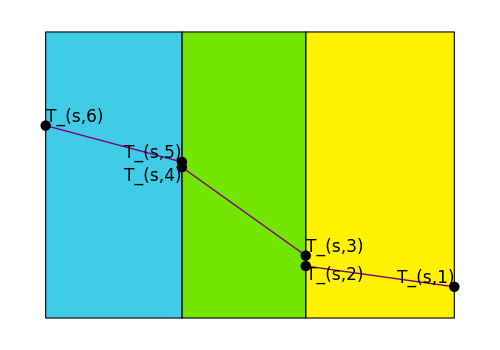





Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX